```mathematica
Phi[x_,xI_,dx_]=Piecewise[{{1-RealAbs[x-xI]/dx, RealAbs[x-xI]<dx}, {0, true}}]
```

Piecewise[{{1-RealAbs[x-xI]/dx, RealAbs[x-xI]<dx}, {0, True}}]

```mathematica
Plot3D[Phi[0,xI,1]Phi[0,yI,1],{xI,-2,2},{yI,-2,2},PlotRange->Full]
```

```mathematica
Plot3D[Phi[0,xI,1]Phi[0,yI,1]
+Phi[0,xI+1,1]Phi[0,yI+1,1]
+Phi[0,xI,1]Phi[0,yI+1,1]
,{xI,-2,2},{yI,-2,2},PlotRange->Full]
```

```mathematica
Grad[Phi[x,xI,h]Phi[y,yI,h],{xI,yI}]
Grad[Phi[0,xI,1]Phi[0,yI,1],{xI,yI}]/.{xI->.5,yI->.2}
```

```mathematica
{(Piecewise[{{1-RealAbs[y-yI]/h, RealAbs[y-yI]<h}, {0, True}}]) (Piecewise[{{1/h, x-xI≥0&&h-x+xI>0}, {-1/h, (x-xI≥0&&h-x+xI>0)||(x-xI<0&&h+x-xI>0)}, {0, True}}]),(Piecewise[{{1-RealAbs[x-xI]/h, RealAbs[x-xI]<h}, {0, True}}]) (Piecewise[{{1/h, y-yI≥0&&h-y+yI>0}, {-1/h, (y-yI≥0&&h-y+yI>0)||(y-yI<0&&h+y-yI>0)}, {0, True}}])}
```

{-0.8,-0.5}

```mathematica
VectorPlot[Grad[Phi[0,xI,1]Phi[0,yI,1],{xI,yI}]/.{xI->x,yI->y},{x,-2,2},{y,-2,2},PlotRange->Full]
```

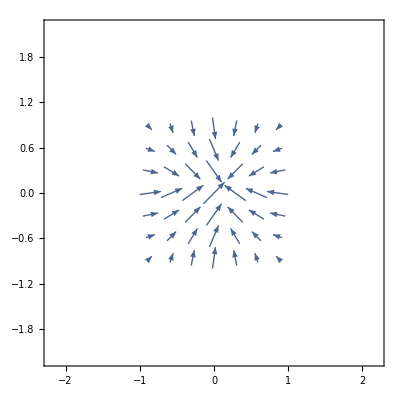

```mathematica
dx0 = 1/128
.25dx0
.75 dx0

{Phi[0,xI,dx0]Phi[0,yI,dx0],
Grad[Phi[0,xI,dx0]Phi[0,yI,dx0],{xI,yI}]}/.{xI->.25dx0,yI->-.75dx0}
```

1/128

0.00195313

0.00585938

{0.1875,{-32.,96.}}